# Problema 10.94

## Datos

```mathematica
(*in Originales 
d2=3;
d3=7;
d4=6;
d4p=6;
d6=7; *)
(*Es importante mencionar que la variable de control paso de ser y5 a θ2 debido a que este cambio ayudara a cumplir los condiciones que se piden*)
(*-----NUEVOS DATOS-----*)
d2=2;
d3=10;
d4=6;
d4p=6;
d6=8;
```

## Ecuaciones cinemáticas

```mathematica
Clear[θ2,θ3,θ4,θ6,y5]
Clear[ω2,ω3,ω4,ω6,vy5]
Clear[α2,α3,α4,α6,ay5]
```

### Ecuaciones de Posición

```mathematica
u2={Cos[θ2], Sin[θ2],0};
u3={Cos[θ3],Sin[θ3],0};
u4={Cos[θ4],Sin[θ4],0};
u6={Cos[θ6],Sin[θ6],0};

RL1={4,-3,0};
RL2={-7,0,0};
R2=d2*u2;
R3=d3*u3;
R4=d4*u4;
R4p=d4p*u4;
R5={0,y5,0};
R6=d6*u6;

(*Lazos vectoriales*)

pos1=RL1+R6+R4+R4p-R5-RL2;
pos2=RL1+R6+R4-R3-R2;
```

### Ecuaciones de velocidad

```mathematica
omega2={0,0,ω2};
omega3={0,0,ω3};
omega4={0,0,ω4};
omega6={0,0,ω6};

V2=omega2×R2;
V3=omega3×R3;
V4=omega4×R4;
V4p=omega4×R4p;
V5={0,vy5,0};
V6=omega6×R6;

(*Lazos vectoriales *)
vel1=V6+V4+V4p-V5;
vel2=V6+V4-V3-V2;
```

### Ecuaciones de Aceleración

```mathematica
alfa2={0,0,α2};
alfa3={0,0,α3};
alfa4={0,0,α4};
alfa6={0,0,α6};

A2=alfa2×R2-ω2^2*R2;
A3=alfa3×R3-ω3^2*R3;
A4=alfa4×R4-ω4^2*R4;
A4p=alfa4×R4p-ω4^2*R4p;
A5={0,ay5,0};
A6=alfa6×R6-ω6^2*R6;

(*Lazos vectoriales *)

acel1=A6+A4+A4p-A5;
acel2=A6+A4-A3-A2;
```

## Solución de Posición

```mathematica
Clear[θ2,θ3,θ4,θ6,y5]
Clear[ω2,ω3,ω4,ω6,vy5]
Clear[α2,α3,α4,α6,ay5]

θ2=105.51*Degree;

SolInicial = FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{y5,1.5},
{θ3,240*Degree},
{θ4,120*Degree},
{θ6,230*Degree}},MaxIterations->15];
SolInicial
```

{y5→-5.00798,θ3→4.58601,θ4→2.62086,θ6→4.6385}

### Solución Total

```mathematica
(*Declaro condiciones iniciales*)
y5i=y5/.SolInicial;
θ3i=θ3/.SolInicial;
θ4i=θ4/.SolInicial;
θ6i=θ6/.SolInicial;


For[i = 10551,i≤46551,i+=100,
θ2=(i/100)*Degree;
SolPos[i]= FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{y5, y5i},
{θ3,θ3i},
{θ4,θ4i},
{θ6, θ6i}},MaxIterations->20];

y5i=y5/.SolPos[i];
θ3i=θ3/.SolPos[i];
θ4i=θ4/.SolPos[i];
θ6i=θ6/.SolPos[i];]
```

## Gráfica de Posición

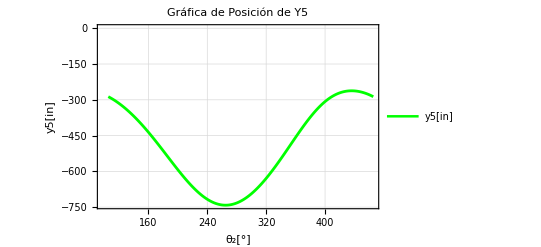

y5[in]

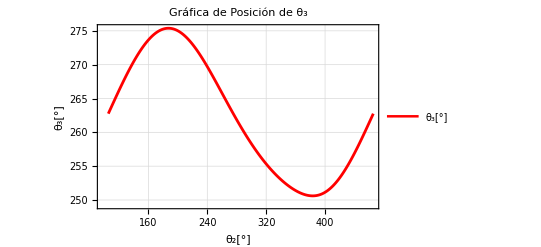

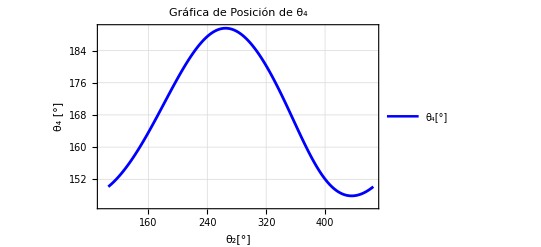

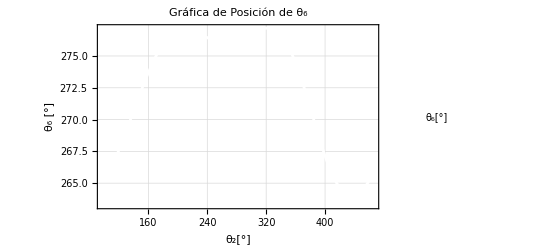

```mathematica
tabla1 = Table[{i/100,(y5/.SolPos[i])/Degree},{i,10551,46551,100}];
tabla2 = Table[{i/100,(θ3/.SolPos[i])/Degree},{i,10551,46551,100}];
tabla3 = Table[{i/100,(θ4/.SolPos[i])/Degree},{i,10551,46551,100}];
tabla4 = Table[{i/100,(θ6/.SolPos[i])/Degree},{i,10551,46551,100}];

ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ_2[°]","y5[in]"},
PlotLabel->"Gráfica de Posición de Y5",
PlotLegends->{"y5[in]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]

y5[in]
ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ_2[°]","θ_3[°]"},
PlotLabel->"Gráfica de Posición de θ_3",
PlotLegends->{"θ_3[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ_2[°]","θ_4 [°]"},
PlotLabel->"Gráfica de Posición de θ_4",
PlotLegends->{"θ_4[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ_2[°]","θ_6 [°]"},
PlotLabel->"Gráfica de Posición de θ_6",
PlotLegends->{"θ_6[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Solución de Velocidad

```mathematica
Clear[θ2,θ3,θ4,θ6,y5]
Clear[ω2,ω3,ω4,ω6,vy5]
Clear[α2,α3,α4,α6,ay5]

ω2=-7.342; (*rad/s*)

For[i = 10551,i≤46551, i+=100,
θ2=(i/100)*Degree;

SolVel[i]= Solve[{
vel1⟦1⟧==0,
vel1⟦2⟧==0,
vel2⟦1⟧==0,
vel2⟦2⟧==0}/.SolPos[i],
{vy5,ω3,ω4,ω6}]//Flatten;];
```

## Gráficas de Velocidad

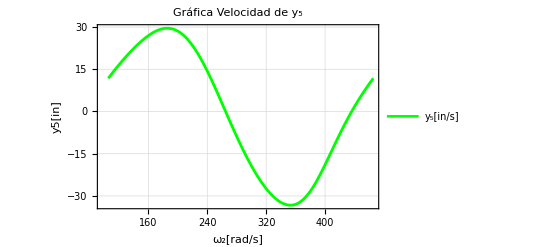

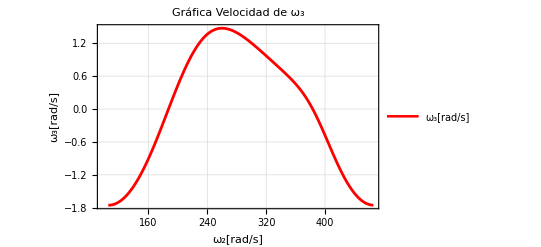

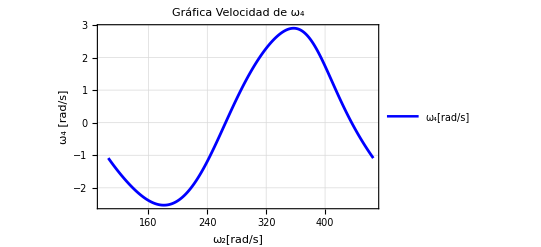

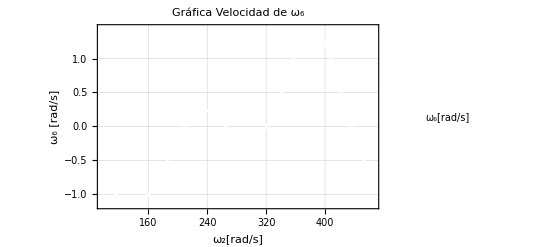

```mathematica
tabla5 = Table[{i/100,vy5/.SolVel[i]},{i,10551,46551,100}];
tabla6 = Table[{i/100,ω3/.SolVel[i]},{i,10551,46551,100}];
tabla7 = Table[{i/100,ω4/.SolVel[i]},{i,10551,46551,100}];
tabla8 = Table[{i/100,ω6/.SolVel[i]},{i,10551,46551,100}];

ListPlot[tabla5,
Frame->True,
FrameLabel->{"ω_2[rad/s]","y5[in]"},
PlotLabel->"Gráfica Velocidad de y_5",
PlotLegends->{"y_5[in/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla6,
Frame->True,
FrameLabel->{"ω_2[rad/s]","ω_3[rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_3",
PlotLegends->{"ω_3[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla7,
Frame->True,
FrameLabel->{"ω_2[rad/s]","ω_4 [rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_4",
PlotLegends->{"ω_4[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla8,
Frame->True,
FrameLabel->{"ω_2[rad/s]","ω_6 [rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_6",
PlotLegends->{"ω_6[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Solución de Aceleración

```mathematica
Clear[θ2,θ3,θ4,θ6,y5]
Clear[ω2,ω3,ω4,ω6,vy5]
Clear[α2,α3,α4,α6,ay5]

ω2=-7.342; 
α2=-0.6478;


For[i = 10551,i≤46551, i+=100,
θ2=(i/100)*Degree;

SolAcel[i]= Solve[{
acel1⟦1⟧==0,
acel1⟦2⟧==0,
acel2⟦1⟧==0,
acel2⟦2⟧==0}/.SolPos[i]/.SolVel[i],
{ay5,α3,α4,α6}]//Flatten;];
```

## Gráficas de Aceleración

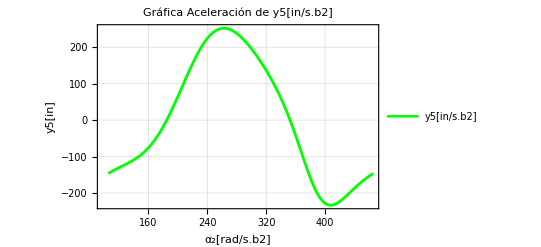

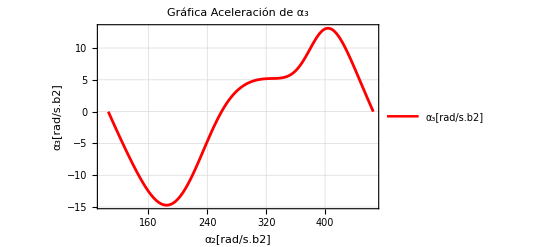

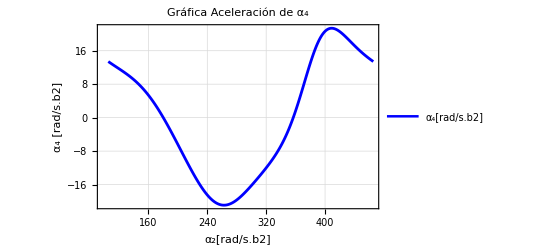

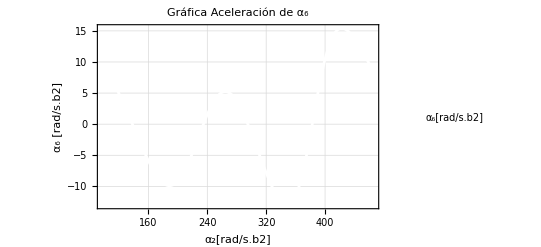

```mathematica
tabla9= Table[{i/100,ay5/.SolAcel[i]},{i,10551,46551,100}];
tabla10= Table[{i/100,α3/.SolAcel[i]},{i,10551,46551,100}];
tabla11= Table[{i/100,α4/.SolAcel[i]},{i,10551,46551,100}];
tabla12= Table[{i/100,α6/.SolAcel[i]},{i,10551,46551,100}];

ListPlot[tabla9,
Frame->True,
FrameLabel->{"α_2[rad/s.b2]","y5[in]"},
PlotLabel->"Gráfica Aceleración de y5[in/s.b2]",
PlotLegends->{"y5[in/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla10,
Frame->True,
FrameLabel->{"α_2[rad/s.b2]","α_3[rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_3",
PlotLegends->{"α_3[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness Subscript[Y, 5][in][0.005]},
ImageSize->400]


ListPlot[tabla11,
Frame->True,
FrameLabel->{"α_2[rad/s.b2]","α_4 [rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_4",
PlotLegends->{"α_4[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla12,
Frame->True,
FrameLabel->{"α_2[rad/s.b2]","α_6 [rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_6",
PlotLegends->{"α_6[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Simulación

```mathematica
Clear[θ2,θ3,θ4,θ6,y5]

Animate[

θ2=(i/100)*Degree;

x={1,0,0};
y={0,1,0};
k={0,0,1};

cero={0,0,0};

(*-----DEFINIENDO GEOMETRICAMENTE-----*)

eslabon2=Cylinder[{cero,R2},0.1]/.SolPos[i];
eslabon3=Cylinder[{R2+0.4*k,R2+R3+0.4*k},0.1]/.SolPos[i];
eslabon4a=Cylinder[{R2+R3+0.6*k,R2+R3+R4p+0.6*k},0.1]/.SolPos[i];
eslabon4b=Cylinder[{R2+R3+0.6*k,R2+R3-R4+0.6*k},0.1]/.SolPos[i];
eslabon5=Cylinder[{R2+R3+R4p+0.4*y,R2+R3+R4p-0.4*y},0.3]/.SolPos[i];
eslabon6=Cylinder[{R2+R3-R4+0.4*y,R2+R3-R4-0.4*y},0.3]/.SolPos[i];


ejeT=Cylinder[{-0.2*k,0.2*k},0.15]/.SolPos[i];
ejeA=Cylinder[{R2-0.2*k,R2+0.8*k},0.15]/.SolPos[i];
ejeB=Cylinder[{R2+R3+0.4*k,R2+R3+0.8*k},0.15]/.SolPos[i];
ejeC=Cylinder[{R2+R3+R4p-0.4*k,R2+R3+R4p+0.7*k},0.15]/.SolPos[i];
ejeD=Cylinder[{R2+R3-R4-0.4*k,R2+R3-R4+0.7*k},0.15]/.SolPos[i];
           
(*-----CARACTERISTICAS-----*)

barra2=Graphics3D[{Purple,eslabon2}];
barra3=Graphics3D[{Red,eslabon3}];
barra4a=Graphics3D[{Green,eslabon4a}];
barra4b=Graphics3D[{Green,eslabon4b}];
deslisador5=Graphics3D[{Yellow,eslabon5}];
deslisador6=Graphics3D[{Orange,eslabon6}];

pernoT=Graphics3D[{Black,ejeT}];
pernoA=Graphics3D[{Black,ejeA}];
pernoB=Graphics3D[{Black,ejeB}];
pernoC=Graphics3D[{Black,ejeC}];
pernoD=Graphics3D[{Black,ejeD}];

Show[barra2,barra3,barra4a,barra4b,deslisador5,deslisador6,pernoT,pernoA,pernoB,pernoC,pernoD,
Axes->True,
AspectRatio->1,
AxesLabel->{"X [in]","Y [in]","Z [in]"},
ImageSize->400,
ViewVertical->{0,1,0},
ViewPoint->{0,0,Infinity},
PlotRange->{{-10,15},{-15,7},{-1,1.3}}
],{i,10551,46551,100},AnimationRunning->False]
```